# Unit 4 · Building Our Own Net

## A transformer that expands ⨂/⨁ expressions, assembled from Units 1–3 — TensorNets units of learning, 4 of 4

© 2026 Computational Classnotes · CC BY-NC-SA 4.0

This unit puts Units 1–3 to work on our own problem. Given an expression such as (a⨁b)⨂c, the net must write its expansion a⨂c ⨁ b⨂c. The data come from Unit 2 (uniform trees, prefix notation, an exact checker), the net from Unit 3 (attention, feed-forward, LayerNorm, positions, shared embeddings, label smoothing, warm-up), and the decoding from Units 1 and 3 (beam search with a length penalty). Evaluate from top to bottom; training (§6) takes about five minutes on a laptop CPU. The write-up “Unit 4 · Building Our Own Net” has the same section numbers.

Before you start: choose Evaluation ▸ Quit Kernel ▸ Local. To skip training, evaluate §1, then the notebook unit4_build_your_own_nets.nb (it defines ownNet), and continue from §7.

## 1. Toolkit

Data and oracle (§3, §4): binaryTree samples uniform binary trees, parseT reads prefix tokens into a tree, infix writes a tree with the fewest parentheses, words and expand compute the exact expansion, equivalentQ checks an answer. The net (§5): the parts of Unit 3, and model, which assembles them. Training (§6): train, with label smoothing and the warm-up schedule. Decoding (§7): beamSearch, with or without the prefix grammar.

```mathematica
(* id: 9eda36b2-b022-4208-9330-25f5203503c7 · unit4_build_your_own · cell 1 of 21 · updated 2026-11-24 07:18 UTC *)
atoms = {"a", "b", "c", "d"}; otimes = "⨂"; oplus = "⨁";     (* the two operator tokens *)
vocab = {"<s>", "</s>", "a", "b", "c", "d", otimes, oplus, "(", ")"};
index = AssociationThread[vocab -> Range[Length[vocab]]];
tArity[t_String] := If[t === otimes || t === oplus, 2, 0];
(* data: uniform binary trees (Unit 2, Algorithm 1), decorated with otimes/oplus and atoms *)
nBin[_, 0] = 1; nBin[0, n_ /; n > 0] = 0;
nBin[e_, n_] := nBin[e, n] = nBin[e - 1, n] + nBin[e + 1, n - 1];
binaryTree[n0_Integer] := Module[{e = 1, n = n0, ks, k, out = {}},
   While[n > 0, ks = Range[0, e - 1]; k = RandomChoice[(nBin[e - # + 1, n - 1] & /@ ks) -> ks];
    out = Join[out, ConstantArray[0, k], {2}]; e = e - k + 1; n--];
   Join[out, ConstantArray[0, e]]];
randomPrefix[n_Integer] := If[# == 2, RandomChoice[{otimes, oplus}], RandomChoice[atoms]] & /@ binaryTree[n];
parseT[tokens_List] := Module[{pos = 1, rec, r},
   rec[] := Module[{t}, If[pos > Length[tokens], Throw[$Failed, tTag]]; t = tokens[[pos++]];
     Which[tArity[t] == 2, {t, rec[], rec[]}, MemberQ[atoms, t], t, True, Throw[$Failed, tTag]]];
   r = Catch[rec[], tTag]; If[r === $Failed || pos <= Length[tokens], $Failed, r]];
(* infix with the fewest parentheses: otimes binds tighter than oplus, so only a oplus under a otimes needs them *)
infix[t_String] := {t};
infix[{"⨁", l_, r_}] := Join[infix[l], {oplus}, infix[r]];
infix[{"⨂", l_, r_}] := Join[paren[l], {otimes}, paren[r]];
paren[x : {"⨁", _, _}] := Join[{"("}, infix[x], {")"}];
paren[x_] := infix[x];
(* the oracle: an expression is a list of words; oplus joins lists, otimes multiplies every word by every word *)
words[t_String] := {{t}};
words[{"⨁", l_, r_}] := Join[words[l], words[r]];
words[{"⨂", l_, r_}] := Flatten[Outer[Join, words[l], words[r], 1], 1];
wordTokens[{w_}] := {w};
wordTokens[w_List] := Join[{otimes, First[w]}, wordTokens[Rest[w]]];
sumTokens[{w_}] := wordTokens[w];
sumTokens[ws_List] := Join[{oplus}, wordTokens[First[ws]], sumTokens[Rest[ws]]];
expand[tree_] := sumTokens[words[tree]];
equivalentQ[tree_, tokens_List] := With[{t = parseT[tokens]}, t =!= $Failed && Sort[words[t]] === Sort[words[tree]]];
makePair[] := Module[{tree, src, tgt}, While[True, tree = parseT[randomPrefix[RandomInteger[{1, 5}]]]; src = infix[tree]; tgt = expand[tree];
    If[Length[src] <= 25 && Length[tgt] <= 40, Return[<|"Tree" -> tree, "Source" -> src, "Target" -> tgt|>]]]];
encode[tokens_List] := index /@ tokens;
(* the net: the parts of Unit 3 *)
mhaNet[d_Integer, h_Integer, causal_ : False] := NetGraph[<|
    "q" -> NetMapOperator[LinearLayer[d]], "k" -> NetMapOperator[LinearLayer[d]], "v" -> NetMapOperator[LinearLayer[d]],
    "rq" -> NetMapOperator[ReshapeLayer[{h, d/h}]], "rk" -> NetMapOperator[ReshapeLayer[{h, d/h}]], "rv" -> NetMapOperator[ReshapeLayer[{h, d/h}]],
    "att" -> If[TrueQ[causal], AttentionLayer["Dot", "MultiHead" -> True, "ScoreRescaling" -> "DimensionSqrt", "Mask" -> "Causal"],
      AttentionLayer["Dot", "MultiHead" -> True, "ScoreRescaling" -> "DimensionSqrt"]],
    "cat" -> NetMapOperator[FlattenLayer[]], "o" -> NetMapOperator[LinearLayer[d]]|>,
   {NetPort["Query"] -> "q" -> "rq" -> NetPort["att", "Query"], NetPort["Memory"] -> "k" -> "rk" -> NetPort["att", "Key"],
    NetPort["Memory"] -> "v" -> "rv" -> NetPort["att", "Value"], "att" -> "cat" -> "o"},
   "Query" -> {"Varying", d}, "Memory" -> {"Varying", d}];
ffnNet[d_Integer, dff_Integer] := NetMapOperator[NetChain[{LinearLayer[dff], Ramp, LinearLayer[d]}], "Input" -> {"Varying", d}];
encoderLayerNet[d_Integer, h_Integer, dff_Integer] := NetGraph[<|
    "att" -> mhaNet[d, h], "add1" -> TotalLayer[], "ln1" -> NormalizationLayer[2, 2], "ffn" -> ffnNet[d, dff], "add2" -> TotalLayer[], "ln2" -> NormalizationLayer[2, 2]|>,
   {NetPort["Input"] -> NetPort["att", "Query"], NetPort["Input"] -> NetPort["att", "Memory"], {NetPort["Input"], "att"} -> "add1" -> "ln1" -> "ffn", {"ln1", "ffn"} -> "add2" -> "ln2"},
   "Input" -> {"Varying", d}];
decoderLayerNet[d_Integer, h_Integer, dff_Integer] := NetGraph[<|
    "self" -> mhaNet[d, h, True], "add1" -> TotalLayer[], "ln1" -> NormalizationLayer[2, 2],
    "cross" -> mhaNet[d, h], "add2" -> TotalLayer[], "ln2" -> NormalizationLayer[2, 2],
    "ffn" -> ffnNet[d, dff], "add3" -> TotalLayer[], "ln3" -> NormalizationLayer[2, 2]|>,
   {NetPort["Input"] -> NetPort["self", "Query"], NetPort["Input"] -> NetPort["self", "Memory"], {NetPort["Input"], "self"} -> "add1" -> "ln1",
    "ln1" -> NetPort["cross", "Query"], NetPort["Memory"] -> NetPort["cross", "Memory"], {"ln1", "cross"} -> "add2" -> "ln2" -> "ffn", {"ln2", "ffn"} -> "add3" -> "ln3"},
   "Input" -> {"Varying", d}, "Memory" -> {"Varying", d}];
freq[d_Integer] := Flatten@Table[{1., 1.}/10000.^(2 i/d), {i, 0, d/2 - 1}];
phase[d_Integer] := Table[If[EvenQ[j], 0., N[Pi/2]], {j, 0, d - 1}];
peNet[d_Integer] := NetGraph[<|"idx" -> SequenceIndicesLayer[], "pos" -> ElementwiseLayer[# - 1. &], "col" -> ReplicateLayer[1, 2],
    "angle" -> NetMapOperator[LinearLayer[d, "Weights" -> List /@ freq[d], "Biases" -> phase[d], LearningRateMultipliers -> 0]],
    "sin" -> ElementwiseLayer[Sin], "add" -> TotalLayer[]|>,
   {NetPort["Input"] -> "idx" -> "pos" -> "col" -> "angle" -> "sin", {NetPort["Input"], "sin"} -> "add"}, "Input" -> {"Varying", d}];
settings = <|"d" -> 32, "heads" -> 4, "dff" -> 128, "layers" -> 2, "smoothing" -> 0.1, "warmup" -> 400,
   "train" -> 12000, "test" -> 100, "rounds" -> 40, "batch" -> 64, "beam" -> 4, "alpha" -> 0.6|>;
(* the whole model: teacher forcing (the decoder reads the target without its last token and predicts it without its first);
   label smoothing by a frozen EmbeddingLayer whose rows are the smoothed targets; one shared array "W" for both embeddings and the output *)
model[s_Association] := Module[{d = s["d"], h = s["heads"], dff = s["dff"], n = s["layers"], V = Length[vocab], ε = s["smoothing"]},
   NetGraph[Join[<|
      "embS" -> EmbeddingLayer[d, V, "Weights" -> NetSharedArray["W"]], "scaleS" -> ElementwiseLayer[Evaluate[Sqrt[N@d]] # &], "peS" -> peNet[d],
      "enc" -> NetChain[Table[encoderLayerNet[d, h, dff], n]],
      "most" -> SequenceMostLayer[],
      "embT" -> EmbeddingLayer[d, V, "Weights" -> NetSharedArray["W"]], "scaleT" -> ElementwiseLayer[Evaluate[Sqrt[N@d]] # &], "peT" -> peNet[d]|>,
     AssociationMap[decoderLayerNet[d, h, dff] &, Table["dec" <> ToString[i], {i, n}]],
     <|"out" -> NetMapOperator[LinearLayer[V, "Weights" -> NetSharedArray["W"]]], "soft" -> SoftmaxLayer[], "rest" -> SequenceRestLayer[],
      "smooth" -> EmbeddingLayer[V, V, "Weights" -> (1 - ε) IdentityMatrix[V] + ε/V, LearningRateMultipliers -> 0],
      "loss" -> CrossEntropyLossLayer["Probabilities"]|>],
    Join[{NetPort["Input"] -> "embS" -> "scaleS" -> "peS" -> "enc", NetPort["Target"] -> "most" -> "embT" -> "scaleT" -> "peT" -> NetPort["dec1", "Input"]},
     Table["enc" -> NetPort["dec" <> ToString[i], "Memory"], {i, n}], Table["dec" <> ToString[i - 1] -> NetPort["dec" <> ToString[i], "Input"], {i, 2, n}],
     {"dec" <> ToString[n] -> "out" -> "soft" -> NetPort["Probabilities"], NetPort["Target"] -> "rest" -> "smooth" -> NetPort["loss", "Target"],
      "soft" -> NetPort["loss", "Input"], "loss" -> NetPort["Loss"]}],
    "Input" -> {"Varying", Restricted["Integer", V]}, "Target" -> {"Varying", Restricted["Integer", V]}]];
trainRate[step_?NumericQ, s_Association] := s["d"]^-0.5 Min[Max[step, 1]^-0.5, Max[step, 1] s["warmup"]^-1.5];
train[s_Association, pairs_List] := Module[{peak = s["d"]^-0.5 s["warmup"]^-0.5},
   NetTrain[NetInitialize@model[s], <|"Input" -> (encode[#Source] & /@ pairs), "Target" -> (encode[Join[{"<s>"}, #Target, {"</s>"}]] & /@ pairs)|>,
    All, LossFunction -> "Loss", BatchSize -> s["batch"], MaxTrainingRounds -> s["rounds"],
    Method -> {"ADAM", "Beta1" -> 0.9, "Beta2" -> 0.98, "LearningRate" -> peak, "LearningRateSchedule" -> (trainRate[#1, s]/peak &)},
    TrainingProgressReporting -> None, TargetDevice -> "CPU"]];
(* decoding: log p(next token) for several prefixes at once; the prefix grammar; beam search with a length penalty *)
nextLogProbs[net_, src_List, prefixes_List] := Log[Clip[Last /@ net[<|"Input" -> ConstantArray[encode[src], Length[prefixes]],
       "Target" -> (Append[encode[#], 1] & /@ prefixes)|>, NetPort["Probabilities"]], {10^-12, 1}]];
need[prefix_List] := 1 + Total[tArity[#] - 1 & /@ Rest[prefix]];
allowed[prefix_List, grammar_] := Which[! TrueQ[grammar], Rest[vocab], need[prefix] == 0, {"</s>"}, True, Join[atoms, {otimes, oplus}]];
beamSearch[net_, src_List, width_Integer, grammar_, α_ : 0.6, maxLen_ : 42] := Module[{beams = {{{"<s>"}, 0.}}, done = {}, lps, cands},
   Do[lps = nextLogProbs[net, src, First /@ beams];
    cands = Flatten[Table[With[{b = beams[[i]], lp = AssociationThread[vocab -> lps[[i]]]},
        Table[{Append[b[[1]], t], b[[2]] + lp[t]}, {t, allowed[b[[1]], grammar]}]], {i, Length[beams]}], 1];
    cands = TakeLargestBy[cands, Last, UpTo[width]];
    done = Join[done, Select[cands, Last[First[#]] === "</s>" &]]; beams = Select[cands, Last[First[#]] =!= "</s>" &];
    If[beams === {} || Length[done] >= width, Break[]], {maxLen}];
   {If[Last[First[#]] === "</s>", Most@Rest@First[#], Rest@First[#]], #[[2]]} & /@ SortBy[If[done === {}, beams, done], -#[[2]]/((5 + Length[#[[1]]])/6.)^α &]];
(* saving a trained net into its own notebook, as one Input cell  ownNet = Uncompress["..."]; *)
saveNet[net_, file_String] := Export[file, Notebook[{Cell[BoxData[RowBox[{
       "(* id: " <> CreateUUID[] <> " · unit4_build_your_own_nets · cell 1 of 1 · updated " <>
        DateString[TimeZoneConvert[Now, 0], {"Year", "-", "Month", "-", "Day", " ", "Hour", ":", "Minute"}] <> " UTC *)", "
",
       RowBox[{"ownNet", "=", RowBox[{"Uncompress", "[", "\"" <> Compress[net] <> "\"", "]"}]}], ";"}]], "Input"]}], "NB"];
SeedRandom[2026];
```

## 2. The task: expand

⨂ distributes over ⨁ on both sides: (A⨁B)⨂C = A⨂C ⨁ B⨂C and A⨂(B⨁C) = A⨂B ⨁ A⨂C. Expanding writes an expression as a ⨁ of words, each word a ⨂-product of atoms. The source is the expression as one would type it; the target is the expansion in prefix notation (Unit 2). The target can be much longer than the source: each ⨂ of two sums multiplies the number of words.

```mathematica
(* id: 1667d165-7a94-47fa-8a9c-47b548f30321 · unit4_build_your_own · cell 2 of 21 · updated 2026-11-24 07:18 UTC *)
examples = Table[makePair[], 5];
Grid[Prepend[{Row[#Source, " "], Row[#Target, " "]} & /@ examples, {"source (infix)", "target (expansion, prefix)"}], Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

source (infix) | target (expansion, prefix)
  a⨁b |   ⨁ab
  c⨂b⨂(a⨁c)⨂b |   ⨁⨂c⨂b⨂ab⨂c⨂b⨂cb
  c⨂c⨂c⨁d |   ⨁⨂c⨂ccd
  d⨁d⨁d⨂(a⨁a⨂a) |   ⨁d⨁d⨁⨂da⨂d⨂aa
  c⨂(b⨁c⨁d) |   ⨁⨂cb⨁⨂cc⨂cd

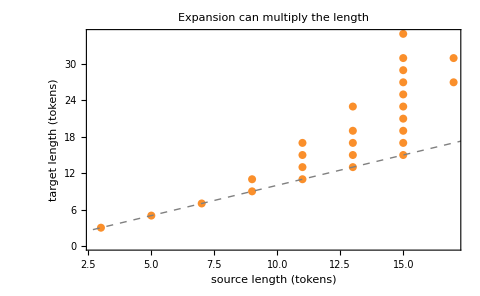

```mathematica
(* id: c2c2cf0b-16a2-4b6f-a01b-037c58e56cd6 · unit4_build_your_own · cell 3 of 21 · updated 2026-11-24 07:18 UTC *)
lengths = Table[With[{p = makePair[]}, {Length[p["Source"]], Length[p["Target"]]}], 3000];
ListPlot[Tally[lengths][[All, 1]], PlotStyle -> Directive[RGBColor[0.98, 0.56, 0.17], PointSize[0.012]], Frame -> True,
 FrameLabel -> {"source length (tokens)", "target length (tokens)"}, PlotLabel -> "Expansion can multiply the length", ImageSize -> 480,
 Epilog -> {Dashed, GrayLevel[0.5], Line[{{0, 0}, {25, 25}}]}, ImagePadding -> {{60, 10}, {40, 30}}]
```

Fig. 1. Source and target lengths for 3000 random pairs (each point is a length pair that occurs). Above the dashed line the expansion is longer than the expression.

```mathematica
(* id: d9dc7677-38a4-4587-84c9-6758a3ee43ee · unit4_build_your_own · cell 4 of 21 · updated 2026-11-24 07:18 UTC *)
N@Mean[Boole[#[[2]] > #[[1]]] & /@ lengths]
```

0.288

Check: the fraction of pairs whose expansion is longer than the source.

## 3. The data

Trees are drawn uniformly with Algorithm 1 of Unit 2, with 1 to 5 operators, each ⨂ or ⨁, over the atoms a, b, c, d. ⨂ binds tighter than ⨁, so the source needs parentheses only around a ⨁ that sits under a ⨂. Pairs with a source over 25 tokens or a target over 40 are dropped.

The tree ⨂(⨁(a, b), c) in prefix is ⨂ ⨁ a b c. In infix, the left child is a ⨁ under a ⨂, so it is bracketed: ( a ⨁ b ) ⨂ c, 7 tokens. The tree ⨁(a, ⨂(b, c)) needs no brackets: a ⨁ b ⨂ c, 5 tokens, because ⨂ binds tighter.

```mathematica
(* id: 6c1f313c-3dd6-42fe-90f6-0ac19f4943ca · unit4_build_your_own · cell 5 of 21 · updated 2026-11-24 07:18 UTC *)
{infix[parseT[{otimes, oplus, "a", "b", "c"}]], infix[parseT[{oplus, "a", otimes, "b", "c"}]]}
```

{{(,a,⨁,b,),⨂,c},{a,⨁,b,⨂,c}}

Check: {{(, a, ⨁, b, ), ⨂, c}, {a, ⨁, b, ⨂, c}}.

```mathematica
(* id: 44918652-fb91-475e-a45c-e37cb1f3186a · unit4_build_your_own · cell 6 of 21 · updated 2026-11-24 07:18 UTC *)
b4 = Select[Tuples[{0, 2}, 9], parseT[# /. {0 -> "a", 2 -> oplus}] =!= $Failed &]; s4 = Counts[Table[binaryTree[4], 14000]];
{Length[b4], Sort[Keys[s4]] == Sort[b4], Min[Values[s4]], Max[Values[s4]]}
```

{14,True,944,1046}

Check: {14, True, min, max}: the sampler reaches all 14 binary trees with four operators, each close to 1000 times in 14 000 samples.

## 4. The oracle

An expression is a list of words. ⨁ joins two lists. ⨂ multiplies every word on the left by every word on the right, keeping their order, because ⨂ is not commutative. Two expressions are equal when their lists of words agree up to order (⨁ is commutative up to isomorphism). This is the check tnEquivalentQ makes in TensorNets.

words(x) = {x}      words(A ⨁ B) = words(A) ∪ words(B)      words(A ⨂ B) = { u v : u ∈ words(A), v ∈ words(B) }

(a⨁b)⨂(c⨁d): words(a⨁b) = {a, b} and words(c⨁d) = {c, d}, so the product gives {ac, ad, bc, bd}: four words of two atoms. In prefix, as a right-nested sum of right-nested products: ⨁ ⨂ a c ⨁ ⨂ a d ⨁ ⨂ b c ⨂ b d, 15 tokens from a source of 11.

```mathematica
(* id: 9106b79c-33c4-42ed-a256-6b7cd5c72447 · unit4_build_your_own · cell 7 of 21 · updated 2026-11-24 07:18 UTC *)
{words[parseT[{otimes, oplus, "a", "b", oplus, "c", "d"}]], expand[parseT[{otimes, oplus, "a", "b", oplus, "c", "d"}]]}
```

{{{a,c},{a,d},{b,c},{b,d}},{⨁,⨂,a,c,⨁,⨂,a,d,⨁,⨂,b,c,⨂,b,d}}

Check: {{{a, c}, {a, d}, {b, c}, {b, d}}, {⨁, ⨂, a, c, ⨁, ⨂, a, d, ⨁, ⨂, b, c, ⨂, b, d}}.

```mathematica
(* id: f237d456-0fa6-4cc7-bb95-559a6859a6aa · unit4_build_your_own · cell 8 of 21 · updated 2026-11-24 07:18 UTC *)
t1 = parseT[{otimes, oplus, "a", "b", "c"}];
{equivalentQ[t1, {oplus, otimes, "b", "c", otimes, "a", "c"}], equivalentQ[t1, {oplus, otimes, "c", "a", otimes, "c", "b"}], AllTrue[Table[makePair[], 500], equivalentQ[#Tree, #Target] &]}
```

{True,False,True}

Check: {True, False, True}: a⨂c ⨁ b⨂c is accepted in either order; c⨂a ⨁ c⨂b is rejected, since the order of factors matters; and for 500 random pairs the target is equivalent to the source.

## 5. The net, assembled from Unit 3

The encoder–decoder of Unit 3, small: d = 32, 4 heads, dff = 128, 2 encoder and 2 decoder layers. Source and target share one vocabulary of 10 tokens, so one array serves the encoder embedding, the decoder embedding and the output projection. The decoder reads the target without its last token and predicts it without its first (teacher forcing). A frozen EmbeddingLayer whose rows are the smoothed targets turns each target index into the label-smoothed distribution (ε = 0.1), and the loss is the cross-entropy against it.

```mathematica
(* id: 5aae147d-796d-4055-956b-f85114a2dc79 · unit4_build_your_own · cell 9 of 21 · updated 2026-11-24 07:18 UTC *)
net0 = NetInitialize@model[settings];
{Information[net0, "ArraysTotalElementCount"], Normal@NetExtract[net0, {"embS", "Weights"}] == Normal@NetExtract[net0, {"embT", "Weights"}] == Normal@NetExtract[net0, {"out", "Net", "Weights"}]}
```

{59950,True}

Counting with the formulas of Unit 3 (d = 32, dff = 128): attention 4(32.b2 + 32) = 4224; feed-forward 32·128 + 128 + 128·32 + 32 = 8352; LayerNorm 64. Encoder layer 4224 + 8352 + 128 = 12 704; decoder layer 2·4224 + 8352 + 192 = 16 992. Two of each: 59 392. The shared embedding adds 10 × 32 = 320 and the output biases 10. The smoothing layer’s 10 × 10 = 100 frozen numbers and the two position layers’ 2 × (32 + 32) = 128 frozen numbers are stored too: 59 392 + 320 + 10 + 100 + 128 = 59 950.

Check: {59950, True}: the count by hand, and one shared array for the three embeddings.

## 6. Training

12 000 training pairs and 100 test pairs, with no test source in the training set. Adam with β₂ = 0.98, the warm-up schedule of Unit 3 with 400 warm-up steps, batches of 64, 40 rounds. This cell takes about five minutes.

```mathematica
(* id: 787c7c35-291f-4c52-b41e-77ae2d085ebc · unit4_build_your_own · cell 10 of 21 · updated 2026-11-24 07:18 UTC *)
test = Table[makePair[], settings["test"]]; testSources = Union[#Source & /@ test];
pairs = {}; While[Length[pairs] < settings["train"], With[{p = makePair[]}, If[! MemberQ[testSources, p["Source"]], AppendTo[pairs, p]]]];
result = train[settings, pairs]; ownNet = result["TrainedNet"]; losses = result["RoundLossList"];
{Length[pairs], Length[test], Round@With[{t = result["TotalTrainingTime"]}, If[QuantityQ[t], QuantityMagnitude[UnitConvert[t, "Seconds"]], t]]}
```

{12000,100,208}

Check: {12000, 100, seconds of training}.

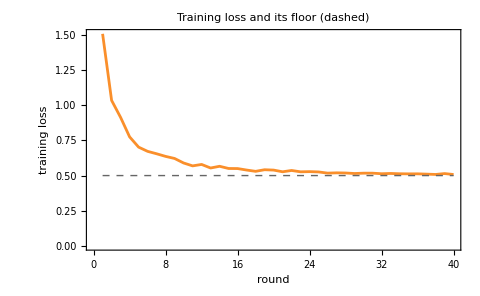

```mathematica
(* id: 553933cb-67cb-4f61-b319-502b13448a3f · unit4_build_your_own · cell 11 of 21 · updated 2026-11-24 07:18 UTC *)
floor = -(0.91 Log[0.91] + 9 0.01 Log[0.01]);
ListLinePlot[losses, PlotStyle -> RGBColor[0.98, 0.56, 0.17], Frame -> True, FrameLabel -> {"round", "training loss"}, PlotRange -> {0, All},
 Epilog -> {Dashed, GrayLevel[0.4], Line[{{1, floor}, {Length[losses], floor}}]}, PlotLabel -> "Training loss and its floor (dashed)", ImageSize -> 480, ImagePadding -> {{60, 10}, {40, 30}}]
```

Fig. 2. The training loss per round. It cannot reach 0: with label smoothing its floor is the entropy of the smoothed target (dashed).

With V = 10 tokens and ε = 0.1 the smoothed target gives 0.91 to the right token and 0.01 to each other. Its entropy is −(0.91 ln 0.91 + 9 × 0.01 ln 0.01) = 0.0858 + 0.4145 = 0.500. A perfect model would score 0.500, not 0.

```mathematica
(* id: fad186b9-90f3-45ff-9bc2-0f0923e2b7e3 · unit4_build_your_own · cell 12 of 21 · updated 2026-11-24 07:18 UTC *)
{floor, First[losses], Last[losses], Last[losses] < First[losses]/2, Last[losses] > floor}
```

{0.500288,1.50872,0.507811,True,True}

Check: {0.500, first loss, last loss, True, True}: the loss fell by more than half and stays above the floor.

## 7. Decoding and checking

Each test source is decoded three ways: greedy (a beam of width 1); a beam of width 4 with the length penalty α = 0.6; and the same beam constrained by the prefix grammar. The grammar uses Unit 2’s counter: </s> is allowed only when the tree is complete, and nothing else is allowed then. Every answer is checked by the oracle. As in Lample and Charton, “any in beam” counts a source as solved if any hypothesis in the beam passes the check.

After ⨁ a the counter is 1 + (2 − 1) + (0 − 1) = 1: one subtree is still owed, so </s> is forbidden and an atom or an operator must follow. After ⨁ a b it is 0: the tree is complete, and only </s> is allowed.

```mathematica
(* id: d84cc609-f87c-4271-932c-da75def2c269 · unit4_build_your_own · cell 13 of 21 · updated 2026-11-24 07:18 UTC *)
{need[{"<s>", oplus, "a"}], allowed[{"<s>", oplus, "a"}, True], need[{"<s>", oplus, "a", "b"}], allowed[{"<s>", oplus, "a", "b"}, True]}
```

{1,{a,b,c,d,⨂,⨁},0,{</s>}}

Check: {1, {a, b, c, d, ⨂, ⨁}, 0, {</s>}}.

```mathematica
(* id: 949c7566-068c-4d92-8a76-f77eb6da9061 · unit4_build_your_own · cell 14 of 21 · updated 2026-11-24 07:18 UTC *)
greedy = beamSearch[ownNet, #Source, 1, False] & /@ test;
free = beamSearch[ownNet, #Source, 4, False] & /@ test;
gram = beamSearch[ownNet, #Source, 4, True] & /@ test;
valid[r_] := N@Mean@Boole[parseT[First@First[#]] =!= $Failed & /@ r];
same[r_] := N@Mean@MapThread[Boole[First@First[#1] === #2["Target"]] &, {r, test}];
top[r_] := N@Mean@MapThread[Boole[equivalentQ[#2["Tree"], First@First[#1]]] &, {r, test}];
any[r_] := N@Mean@MapThread[Boole[AnyTrue[First /@ #1, Function[h, equivalentQ[#2["Tree"], h]]]] &, {r, test}];
Grid[Prepend[{#1, PercentForm[valid[#2]], PercentForm[same[#2]], PercentForm[top[#2]], PercentForm[any[#2]]} & @@@
   {{"greedy", greedy}, {"beam 4", free}, {"beam 4 + grammar", gram}},
  {"decoding (100 test sources)", "valid prefix", "same tokens as the oracle", "top answer verified", "any in beam verified"}], Frame -> All, Background -> {None, {LightGray}}]
```

decoding (100 test sources) | valid prefix | same tokens as the oracle | top answer verified | any in beam verified
greedy | 100% | 86% | 86% | 86%
beam 4 | 100% | 84% | 84% | 94%
beam 4 + grammar | 100% | 87% | 87% | 97%

```mathematica
(* id: 4fe799b6-a134-4686-a974-31f2812aded3 · unit4_build_your_own · cell 15 of 21 · updated 2026-11-24 07:18 UTC *)
{valid[gram] == 1., any[gram] >= top[gram], any[free] >= top[free]}
```

{True,True,True}

Check: {True, True, True}: with the grammar every answer is a valid tree, and “any in beam” is never below “top answer”, since it counts the top answer too.

```mathematica
(* id: df5facd3-bb52-49a5-a341-f14e79fb181b · unit4_build_your_own · cell 16 of 21 · updated 2026-11-24 07:18 UTC *)
Grid[Prepend[Table[{Row[test[[i]]["Source"], " "], Row[First@First[gram[[i]]], " "], equivalentQ[test[[i]]["Tree"], First@First[gram[[i]]]]}, {i, 6}],
  {"source", "top answer (beam 4 + grammar)", "verified"}], Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

source | top answer (beam 4 + grammar) | verified
  a⨂(d⨂a⨁a⨁b)⨁c |   ⨁⨂a⨂da⨁⨂aa⨁⨂abc | True
  a⨂b⨁b⨂a |   ⨁⨂ab⨂ba | True
  a⨁a |   ⨁aa | True
  (b⨁b⨂b⨁a)⨂c |   ⨁⨂bc⨁⨂b⨂bc⨂ac | True
  a⨂(b⨁b)⨁c⨂(c⨁d) |   ⨁⨂ab⨁⨂ab⨁⨂bc⨁⨂cd⨂ac | False
  a⨂a |   ⨂aa | True

## 8. Where the net goes wrong

The oracle shows exactly which answers are wrong. Group the test sources by the length of their expansion and compare the top-answer accuracy:

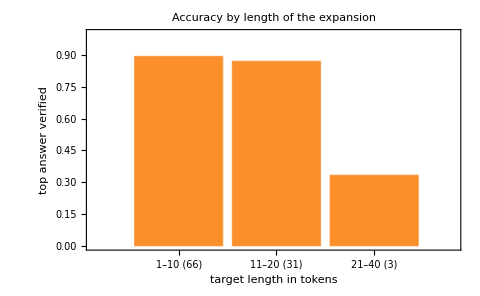

```mathematica
(* id: afab7108-f11c-49c0-847b-5fed3877847f · unit4_build_your_own · cell 17 of 21 · updated 2026-11-24 07:18 UTC *)
byLen = GroupBy[Transpose[{Length[#Target] & /@ test, MapThread[Boole[equivalentQ[#2["Tree"], First@First[#1]]] &, {gram, test}]}],
   Which[#[[1]] <= 10, "1–10", #[[1]] <= 20, "11–20", True, "21–40"] & -> Last];
byLen = KeyTake[byLen, {"1–10", "11–20", "21–40"}];
BarChart[N[Mean /@ Values[byLen]], ChartLabels -> KeyValueMap[#1 <> " (" <> ToString[Length[#2]] <> ")" &, byLen],
 ChartStyle -> RGBColor[0.98, 0.56, 0.17], PlotRange -> {0, 1}, Frame -> True, FrameLabel -> {"target length in tokens", "top answer verified"},
 PlotLabel -> "Accuracy by length of the expansion", ImageSize -> 480, ImagePadding -> {{60, 10}, {40, 30}}]
```

Fig. 3. Top-answer accuracy (beam 4 + grammar) on the test sources, grouped by the length of the correct expansion.

```mathematica
(* id: 1f54e1a1-8f7f-43f8-be70-3928d83ddd83 · unit4_build_your_own · cell 18 of 21 · updated 2026-11-24 07:18 UTC *)
{Length /@ byLen, N[Mean /@ byLen]}
```

{<|1–10→66,11–20→31,21–40→3|>,<|1–10→0.893939,11–20→0.870968,21–40→0.333333|>}

Check: the number of test sources in each group, and the accuracy of each. A single wrong token spoils a whole expansion, so longer targets are harder.

```mathematica
(* id: 79353432-2036-4a14-b231-b855c729ff6e · unit4_build_your_own · cell 19 of 21 · updated 2026-11-24 07:18 UTC *)
wrong = Select[Range[Length[test]], ! equivalentQ[test[[#]]["Tree"], First@First[gram[[#]]]] &];
Grid[Prepend[Table[{Row[test[[i]]["Source"], " "], Row[test[[i]]["Target"], " "], Row[First@First[gram[[i]]], " "]}, {i, Take[wrong, UpTo[6]]}],
  {"source", "correct expansion", "the net’s answer"}], Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

source | correct expansion | the net’s answer
  a⨂(b⨁b)⨁c⨂(c⨁d) |   ⨁⨂ab⨁⨂ab⨁⨂cc⨂cd |   ⨁⨂ab⨁⨂ab⨁⨂bc⨁⨂cd⨂ac
  a⨂d⨂c |   ⨂a⨂dc |   ⨂a⨂d⨂cc
  b⨂a⨂c |   ⨂b⨂ac |   ⨂b⨂a⨂cc
  d⨂d⨂a |   ⨂d⨂da |   ⨂d⨂d⨂aa
  c⨂(b⨁d⨁b⨂a) |   ⨁⨂cb⨁⨂cd⨂c⨂ba |   ⨁⨂cb⨁⨂cd⨂c⨂aa
  (b⨁c⨂d)⨂c⨂c⨂a |   ⨁⨂b⨂c⨂ca⨂c⨂d⨂c⨂ca |   ⨁⨂b⨂c⨂ca⨂c⨂d⨂c⨂c⨂aa

## 9. Saving the net

The trained net goes into its own notebook, unit4_build_your_own_nets.nb, as one Input cell ownNet = Uncompress["…"]. Evaluating that notebook brings the net back without training.

```mathematica
(* id: 3c3b8b81-873c-4691-b645-075a5ad17584 · unit4_build_your_own · cell 20 of 21 · updated 2026-11-24 07:18 UTC *)
saveNet[ownNet, FileNameJoin[{Quiet@Check[NotebookDirectory[], Directory[]], "unit4_build_your_own_nets.nb"}]];
First@First@beamSearch[ownNet, Characters["(a⨁b)⨂c"], 4, True]
```

{⨁,⨂,a,c,⨂,b,c}

Check: {⨁, ⨂, a, c, ⨂, b, c}: the saved net expands (a⨁b)⨂c to a⨂c ⨁ b⨂c. Characters splits a typed expression into tokens, since every symbol is one character.

## 10. Exercises

1. Expand a⨂(b⨁c)⨂d by hand, and count its words.

2. How many words has (a⨁b)⨂(c⨁d)⨂(a⨁b)? How long is its expansion in prefix tokens?

3. What would the loss floor of §6 be with ε = 0.2?

4. Ask the net to expand an expression of your own, and check its answer with equivalentQ.

5. What does the grammar allow after ⨂ ⨁ a b?

Answers, computed:

```mathematica
(* id: 7def9994-1efd-40b3-a123-04744aef791f · unit4_build_your_own · cell 21 of 21 · updated 2026-11-24 07:18 UTC *)
{words[parseT[{otimes, "a", otimes, oplus, "b", "c", "d"}]],
 {Length@words[parseT[{otimes, oplus, "a", "b", otimes, oplus, "c", "d", oplus, "a", "b"}]], Length@expand[parseT[{otimes, oplus, "a", "b", otimes, oplus, "c", "d", oplus, "a", "b"}]]},
 -(0.82 Log[0.82] + 9 0.02 Log[0.02]),
 With[{src = Characters["a⨂(b⨁c)"]}, {First@First@beamSearch[ownNet, src, 4, True], equivalentQ[parseT[{otimes, "a", oplus, "b", "c"}], First@First@beamSearch[ownNet, src, 4, True]]}],
 allowed[{"<s>", otimes, oplus, "a", "b"}, True]}
```

{{{a,b,d},{a,c,d}},{8,47},0.866894,{{⨁,⨂,a,b,⨂,a,c},True},{a,b,c,d,⨂,⨁}}

1: {abd, acd}, two words. 2: 8 words of 3 atoms; the expansion has 8 × 5 + 7 = 47 prefix tokens, more than the 40 allowed in training, so the net has never seen one so long. 3: 0.867. 4: the net’s answer for a⨂(b⨁c) and its check. 5: one subtree is still owed (the right factor), so an atom or an operator, but not </s>.

## 11. Summary

Every part came from the earlier units. Unit 2 gave the data: uniform trees, prefix targets and an exact oracle. Unit 3 gave the net, built from primitive Wolfram layers, with shared embeddings, label smoothing and warm-up. Units 1 and 3 gave the decoding: beam search with a length penalty, here constrained by the prefix grammar. The oracle makes the net safe to use: an answer that fails the check is never accepted, and the beam gives several chances.

In TensorNets: tnParserNet in ff_tensornets_new.nb is this kind of encoder–decoder, mapping tokens to the prefix tree; tnPolicyNet and tnValueNet reuse the encoder. There, simplification is done by the policy net choosing rewrite rules that the exact engine applies, so every step is sound, rather than by writing the whole answer at once as here.

© 2026 Computational Classnotes · CC BY-NC-SA 4.0